# GS-LS Algorithm

#### Yibin Jiang, Abhishek Sharma Cronin Lab University of Glasgow

## Define functions

```mathematica
Unprotect[$MachinePrecision];
$MachinePrecision=100;
Protect[$MachinePrecision];
```

```mathematica
LaunchKernels[8];
ObjectiveFunction[X_] := Module[{performance,attribute},
(*Define a objective function to map input (X) to a performance and attribute space (Y)*)
performance = Total[X,{2}];
attribute = Round[X⟦All,1⟧/0.1];
Return[Transpose[{performance,attribute}]]
]

IntializePool[X_,Y_]:=Module[{pool,indexes,Xtemp,Ytemp,Maxindex,Sample},
(*create the initial pool according to the attribute*)
pool = {};
Table[
indexes =Flatten[Position[Y⟦All,-1⟧,attributeIndex]];
Xtemp = X⟦indexes⟧;
Ytemp = Y⟦indexes⟧;
Maxindex = Ordering[Ytemp⟦All,1⟧]⟦-1⟧;
Sample = Join[Xtemp⟦Maxindex⟧,Ytemp⟦Maxindex⟧];
AppendTo[pool,Sample],
{attributeIndex,DeleteDuplicates[Y⟦All,-1⟧]}];
Return[pool];
]
CrossOver[pool_,featureNum_]:=Module[{indexes,offspring},
indexes =RandomInteger[{1,Length[pool]},2] ;
(*Print[pool⟦indexes⟧//MatrixForm];*)
offspring = Table[Flatten[pool⟦indexes⟦RandomInteger[{1,2},1]⟧⟧]⟦i⟧,{i,featureNum}];
(*Print[offspring];*)
Return[offspring]
]
Mutation[offspringOrgi_,sigma_]:=Module[{indexes,offspring},
offspring = offspringOrgi+RandomVariate[NormalDistribution[0,sigma],{Length[offspringOrgi]}];
Return[offspring]
]
```

```mathematica
GenerateSamples[pool_,featureNum_,sigma_,mutationRate_,{batchSizeC_,batchSizeM_,batchSizeR_}]:=Module[{samples,offspring},
samples = {};
(*Crossover + Mutation*)
Table[
offspring = CrossOver[pool,featureNum];
If[RandomReal[]<mutationRate,
offspring = Mutation[offspring,sigma]
];
AppendTo[samples,offspring],
{i,batchSizeC}];
(*Mutation*)
Table[
offspring = pool⟦RandomInteger[{1,Length[pool]}]⟧⟦1;;featureNum⟧;
offspring = Mutation[offspring,sigma];
AppendTo[samples,offspring],
{i,batchSizeM}];
(*Random sampling*)
Table[
offspring =Flatten[RandomReal[{0,1},{1,featureNum}]]; 
AppendTo[samples,offspring],
{i,batchSizeR}];
Return[samples]
]
```

```mathematica
UpdatePool[samples_,pool_]:=Module[{indexes,poolindexes,poolelite,samplesTemp,Maxindex,elite,originalpool},
originalpool=pool;
Table[
indexes =Flatten[Position[samples⟦All,-1⟧,attributeIndex]];
poolindexes =Flatten[Position[pool⟦All,-1⟧,attributeIndex]];
poolelite = Flatten[pool⟦poolindexes⟧];
samplesTemp = samples⟦indexes⟧;
Maxindex = Ordering[samplesTemp⟦All,-2⟧]⟦-1⟧;
elite = Flatten[samplesTemp⟦Maxindex⟧];
Which[Length[poolindexes]<1,
AppendTo[originalpool,elite],
elite⟦-2⟧>poolelite⟦-2⟧,
originalpool⟦poolindexes⟧ = elite
],
{attributeIndex,DeleteDuplicates[samples⟦All,-1⟧]}];
Return[originalpool]
]
```

```mathematica
fromXtoSpectrum1[X_,Qset_]:=Module[{gridweights,standardD,spectrum,griddistance},
griddistance = Table[((X⟦1⟧-i)^2+(X⟦2⟧-j)^2+(X⟦3⟧-k)^2)^(1/2),{i,Subdivide[0,1,(Dimensions@shapes)⟦1⟧-1]},{j,Subdivide[0,1,(Dimensions@shapes)⟦2⟧-1]},{k,Subdivide[0,1,(Dimensions@shapes)⟦3⟧-1]}];
gridweights =N[PDF[NormalDistribution[0,0.0001+0.08*X⟦4⟧],griddistance]];
If[Total[Flatten[gridweights]]>0,
gridweights = gridweights/Total[Flatten[gridweights]]];
spectrum = 0;
Table[spectrum = spectrum +gridweights⟦i,j,k⟧*Qset⟦i,j,k,All⟧,{i,1,(Dimensions@gridweights)⟦1⟧},{j,1,(Dimensions@gridweights)⟦2⟧},{k,1,(Dimensions@gridweights)⟦3⟧}];
Return[spectrum]
]
```

```mathematica
fromXtoSpectrum2[X_,Qset_]:=Module[{gridweights,standardD,spectrum,griddistance},

spectrum =(1-X⟦5⟧)*Qset⟦Round[X⟦1⟧/(1/8)]+1,Round[X⟦2⟧/(1/10)]+1,Round[X⟦3⟧/(1/10)]+1,Round[X⟦4⟧/(1/3)]+1,All⟧ +X⟦5⟧Qset⟦1,1,1,1,All⟧;
Return[spectrum]
]
```

```mathematica
fromSpetrumtoY[data_]:=Module[{rescaleddata,peaks,prominences,class,fitness,boundary1,boundary2,fitness1,fitness2,function,figure},
rescaleddata = Rescale[data];
peaks = FindPeaks[rescaleddata];
peaks⟦All,1⟧ = Round[peaks⟦All,1⟧ ];
prominences = Prominence[wavelength,rescaleddata,peaks];
peaks = peaks⟦Flatten[Position[prominences,_?(#>0.01&)]]⟧;
prominences = prominences⟦Flatten[Position[prominences,_?(#>0.01&)]]⟧;
If[Length[prominences] ==0,Return[{0,False}]];
Which[Length[prominences] ==1,
class = Ceiling[(wavelength⟦peaks⟦1⟧⟦1⟧⟧ - Min[wavelength])/0.05];
fitness =1/Total[rescaleddata] Total[rescaleddata⟦Select[Table[i,{i,Length[wavelength]}],wavelength⟦peaks⟦1⟧⟦1⟧⟧ -0.05<wavelength⟦#⟧&&wavelength⟦#⟧<wavelength⟦peaks⟦1⟧⟦1⟧⟧ +0.05&]⟧] ,
Length[prominences] ≥2,

peaks = peaks⟦Ordering[prominences,-2]⟧;
prominences = prominences⟦Ordering[prominences,-2]⟧;
class =Ceiling[(wavelength⟦peaks⟦All,1⟧⟧ - Min[wavelength])/0.05];
boundary1 = Select[Table[i,{i,Length[wavelength]}],wavelength⟦peaks⟦1⟧⟦1⟧⟧ -0.05<wavelength⟦#⟧&&wavelength⟦#⟧<wavelength⟦peaks⟦1⟧⟦1⟧⟧ +0.05&];
boundary2 = Select[Table[i,{i,Length[wavelength]}],wavelength⟦peaks⟦2⟧⟦1⟧⟧ -0.05<wavelength⟦#⟧&&wavelength⟦#⟧<wavelength⟦peaks⟦2⟧⟦1⟧⟧ +0.05&];
fitness1 =Total[rescaleddata⟦Union[boundary1,boundary2]⟧]/Total[rescaleddata];
fitness2= Total[rescaleddata⟦boundary2⟧]/Total[rescaleddata];
];
function = Interpolation[Transpose[{wavelength,rescaleddata}]];
figure = ListLinePlot[Transpose[{wavelength,rescaleddata}],PlotStyle->Directive[Blue],Epilog->{Red,Table[Line[{{i⟦1⟧,0},i}],{i,Transpose[{wavelength⟦peaks⟦All,1⟧⟧,peaks⟦All,2⟧}]}]},PlotRange->All];
Which[Length[prominences] ==1,
Return[{1,figure,fitness,class}],
Length[prominences] ≥2,
Return[{2,figure,{fitness1,fitness2},class}]
]
]
Prominence[wavelength_,rescaleddata_,peaks_]:=Module[{function,plot,prominences,solutions,leftBasis,rightBasis,leftwavelengths,rightwavelengths,leftHeight,rightHeight,prominence},
function = Interpolation[Transpose[{wavelength,rescaleddata}]];
prominences = 
Table[plot = Plot[function[x],{x,Min[wavelength],Max[wavelength]},Mesh->{{peaks⟦i⟧⟦2⟧}},MeshFunctions->{#2&},MeshStyle->PointSize[Medium],PlotRange->All,PlotPoints->10000];
solutions=Sort@Cases[Normal@plot,Point[{x_,y_}]->x,Infinity];
solutions = DeleteCases[solutions,x_/;Abs[x -wavelength⟦peaks⟦i⟧⟦1⟧⟧]≤0.01];
leftBasis =Max[Max[ DeleteCases[solutions,x_/;x>wavelength⟦peaks⟦i⟧⟦1⟧⟧]],Min[wavelength]];
rightBasis = Min[Min[DeleteCases[solutions,x_/;x<wavelength⟦peaks⟦i⟧⟦1⟧⟧]],Max[wavelength]];
leftwavelengths= Select[wavelength,leftBasis≤#≤wavelength⟦peaks⟦i⟧⟦1⟧⟧&];
rightwavelengths=Select[wavelength,wavelength⟦peaks⟦i⟧⟦1⟧⟧≤#≤rightBasis&] ;
leftHeight=Min[function[leftwavelengths]];
rightHeight=Min[function[rightwavelengths]];
prominence = Min[peaks⟦i⟧⟦2⟧ - leftHeight,peaks⟦i⟧⟦2⟧ - rightHeight],{i,Length[peaks]}];
Return[prominences]]
```

```mathematica
ObjectiveFunction2[X_,Qset_]:=Module[{data,Y,results,XNew,YNew,figures},
data = Table[fromXtoSpectrum2[X⟦i⟧,Qset],{i,(Dimensions@X)⟦1⟧}];
Y = Table[
fromSpetrumtoY[data⟦j⟧],{j,Length[data]}];
results = {};
Table[
Which[
(*Y⟦i⟧⟦1⟧ ==1,
AppendTo[results,{X⟦i⟧,Y⟦i⟧}],*)
Y⟦i⟧⟦1⟧ ==2,
AppendTo[results,{X⟦i⟧,Flatten[{Y⟦i⟧⟦1;;2⟧,Y⟦i⟧⟦3⟧⟦2⟧,Y⟦i⟧⟦4⟧⟦2⟧}]}]
(*AppendTo[results,{X⟦i⟧,Flatten[{Y⟦i⟧⟦1;;2⟧,Y⟦i⟧⟦3⟧⟦1⟧,100*Y⟦i⟧⟦4⟧⟦1⟧+Y⟦i⟧⟦4⟧⟦2⟧}]}];
AppendTo[results,{X⟦i⟧,Flatten[{Y⟦i⟧⟦1;;2⟧,Y⟦i⟧⟦3⟧⟦2⟧,10000*Y⟦i⟧⟦4⟧⟦1⟧+Y⟦i⟧⟦4⟧⟦2⟧}]}]*)],{i,Length[Y]}];
XNew = results⟦All,1⟧;
YNew = results⟦All,2⟧⟦All,-2;;⟧;
figures = results⟦All,2⟧⟦All,-3⟧;
Return[{XNew,YNew,figures}]
]
```

```mathematica
fromSpetrumtoY2[data_,target_]:=Module[{Targetpeak,rescaledtarget,rescaleddata,peaks,prominences,class,fitness,boundary1,boundary2,fitness1,fitness2,fitness3,function,figure},
(*Rescale target and current data*)
rescaleddata = Rescale[data];
rescaledtarget =  Rescale[target];
(*Obtain target peak positions*)
Targetpeak = wavelength⟦Flatten[Position[rescaledtarget,Max[rescaledtarget]]]⟦1⟧⟧;
peaks = FindPeaks[rescaleddata];
peaks⟦All,1⟧ = Round[peaks⟦All,1⟧ ];
prominences = Prominence[wavelength,rescaleddata,peaks];
peaks = peaks⟦Flatten[Position[prominences,_?(#>0.01&)]]⟧;
prominences = prominences⟦Flatten[Position[prominences,_?(#>0.01&)]]⟧;
If[Length[prominences] ==0,Return[{0,False}]];
Which[Length[prominences] ==1,
class = Ceiling[(wavelength⟦peaks⟦1⟧⟦1⟧⟧ - Min[wavelength])/0.05];
fitness =1/Total[rescaleddata] Total[rescaleddata⟦Select[Table[i,{i,Length[wavelength]}],wavelength⟦peaks⟦1⟧⟦1⟧⟧ -0.05<wavelength⟦#⟧&&wavelength⟦#⟧<wavelength⟦peaks⟦1⟧⟦1⟧⟧ +0.05&]⟧] ,
Length[prominences] ≥2,

peaks = peaks⟦Ordering[prominences,-2]⟧;
prominences = prominences⟦Ordering[prominences,-2]⟧;
class =Ceiling[(wavelength⟦peaks⟦All,1⟧⟧ - Min[wavelength])/0.05];
boundary1 = Select[Table[i,{i,Length[wavelength]}],wavelength⟦peaks⟦1⟧⟦1⟧⟧ -0.05<wavelength⟦#⟧&&wavelength⟦#⟧<wavelength⟦peaks⟦1⟧⟦1⟧⟧ +0.05&];
boundary2 = Select[Table[i,{i,Length[wavelength]}],wavelength⟦peaks⟦2⟧⟦1⟧⟧ -0.05<wavelength⟦#⟧&&wavelength⟦#⟧<wavelength⟦peaks⟦2⟧⟦1⟧⟧ +0.05&];
fitness1 =Total[rescaleddata⟦Union[boundary1,boundary2]⟧]/Total[rescaleddata];
fitness2= Total[rescaleddata⟦boundary2⟧]/Total[rescaleddata];
fitness3 =- 0.2*Total[Abs[rescaleddata - rescaledtarget]] - Abs[(wavelength⟦peaks⟦2,1⟧⟧ - Targetpeak)]
];
function = Interpolation[Transpose[{wavelength,rescaleddata}]];
figure = ListLinePlot[Transpose[{wavelength,rescaleddata}],PlotStyle->Directive[Blue],Epilog->{Red,Table[Line[{{i⟦1⟧,0},i}],{i,Transpose[{wavelength⟦peaks⟦All,1⟧⟧,peaks⟦All,2⟧}]}]},PlotRange->All];
Which[Length[prominences] ==1,
Return[{1,figure,fitness,class}],
Length[prominences] ≥2,
Return[{2,figure,{fitness1,fitness2,fitness3},class}]
]
]
```

```mathematica
ObjectiveFunction3[X_,Qset_,targetX_]:=Module[{data,Y,results,XNew,YNew,figures,target},
data = Table[fromXtoSpectrum2[X⟦i⟧,Qset],{i,(Dimensions@X)⟦1⟧}];
target = fromXtoSpectrum2[targetX,Qset];
Y = Table[
fromSpetrumtoY2[data⟦j⟧,target],{j,Length[data]}];
results = {};
Table[
Which[
(*Y⟦i⟧⟦1⟧ ==1,
AppendTo[results,{X⟦i⟧,Y⟦i⟧}],*)
Y⟦i⟧⟦1⟧ ==2,
AppendTo[results,{X⟦i⟧,Flatten[{Y⟦i⟧⟦1;;2⟧,Y⟦i⟧⟦3⟧⟦3⟧,Y⟦i⟧⟦4⟧⟦2⟧}]}]
(*AppendTo[results,{X⟦i⟧,Flatten[{Y⟦i⟧⟦1;;2⟧,Y⟦i⟧⟦3⟧⟦1⟧,100*Y⟦i⟧⟦4⟧⟦1⟧+Y⟦i⟧⟦4⟧⟦2⟧}]}];
AppendTo[results,{X⟦i⟧,Flatten[{Y⟦i⟧⟦1;;2⟧,Y⟦i⟧⟦3⟧⟦2⟧,10000*Y⟦i⟧⟦4⟧⟦1⟧+Y⟦i⟧⟦4⟧⟦2⟧}]}]*)],{i,Length[Y]}];
XNew = results⟦All,1⟧;
YNew = results⟦All,2⟧⟦All,-2;;⟧;
figures = results⟦All,2⟧⟦All,-3⟧;
Return[{XNew,YNew,figures}]
]
```

## Run tests

```mathematica
wavelength = Table[i,{i,400,900,400/999}]/1000;
shapes = ParallelTable[ToString[k]<>"_"<>ToString[i]<>"_"<>ToString[j],{k,20,60,5},{i,1,3,0.2},{j,1,3,0.2}];
randomshapes = shapes;
```

```mathematica
Qset=Import[NotebookDirectory[]<>"Qset.mx"]; (* Import the spectral data from the previous exploration*)
```

```mathematica
TargetX = {0.8,0.8,0.8,0,0};
```

```mathematica
Observations=Import[NotebookDirectory[]<>"Observations"<>".mx"]; (* Processed data after comparing the data from exploration and the target spectrum*)
```

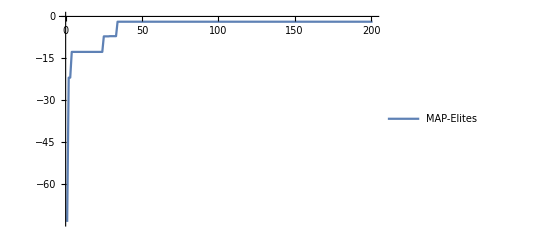

```mathematica
MAPEliteFitnessAll=Table[Max[Flatten@Table[Observations⟦i⟧⟦2⟧⟦All,1⟧,{i,j}]],{j,201}]
ListLinePlot[MAPEliteFitnessAll,PlotRange->Full,PlotLegends->{"MAP-Elites"}]
```

```mathematica
ObservationsXI = Table[Observations⟦i⟧⟦1⟧,{i,201}];
ObservationsYI = Table[Observations⟦i⟧⟦2⟧⟦All,1⟧,{i,201}];
Position[ObservationsYI,Max[ObservationsYI]]
```

{{34,10},{63,10},{75,1},{188,8}}

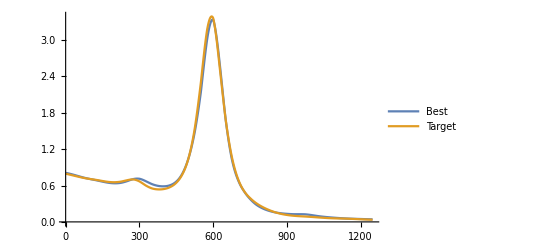

```mathematica
ListLinePlot[{fromXtoSpectrum2[ObservationsXI⟦34,10⟧,Qset],fromXtoSpectrum2[TargetX,Qset]},PlotRange->Full,PlotLegends->{"Best","Target"}]
```

```mathematica
RunNS[Observations_,initialStep_]:=Module[{ObservationsXI,ObservationsYI,featureNum,initialNum,batchSizeC,batchSizeM,batchSizeR,sigma,mutationRate,X,Y,NoveltyResultsTotal},
ObservationsXI = Table[Observations⟦i⟧⟦1⟧,{i,initialStep}];
ObservationsYI = Table[Observations⟦i⟧⟦2⟧⟦All,1⟧,{i,initialStep}];
featureNum = 5; (* the number of feature of the input space*)
initialNum = 10; (* the initial sampling number*)
batchSizeC = 10;(* crossover+ mutation *)
batchSizeM = 10; (* mutation *)
batchSizeR = 3;(* random sampling*)
sigma = 0.15;(* the standard deviation of noise in mutation *)
mutationRate = 0.4;(* the probability of mutation *)
X = ArrayReshape[ObservationsXI,{(Length@Flatten@ObservationsXI)/featureNum,featureNum}];
Y =  ArrayReshape[ObservationsYI,{(Length@Flatten@ObservationsYI)/1,1}];
NoveltyResultsTotal =ParallelTable[
SeedRandom[count];
SampleResultsTotal={};
ObservationsX = {};
ObservationsY = {};
samplesInput=X;
sampleResult =Y;
AppendTo[ObservationsX,samplesInput];
AppendTo[ObservationsY,sampleResult];
AppendTo[SampleResultsTotal,Join[samplesInput,sampleResult,2]];
NoveltyResults  =Table[
ObservationsX = ArrayReshape[ObservationsX,{Length[Flatten@ObservationsX]/featureNum,featureNum}];
ObservationsY = Flatten@ObservationsY;
NoveltyNumber = 10;
Novelty = Table[Mean[Sort[Flatten@Outer[EuclideanDistance,{ObservationsX⟦i⟧},DeleteDuplicates@ObservationsX,1]]⟦1;;NoveltyNumber⟧],{i,Length[ObservationsX]}];
ObservationsYTrue = ObservationsY + Novelty*100;(*the Novelty term is equavilent to the local sparseness term desribed in the paper; here the code was shown with coefficeint of 100*)
pool = DeleteDuplicates[ObservationsX⟦Ordering[-Round[ObservationsYTrue,10^-10]]⟧]⟦1;;5⟧;
samplesInput= GenerateSamples[pool,featureNum,sigma,mutationRate,{batchSizeC,batchSizeM,batchSizeR}];
samplesInput = samplesInput/.n_?NumericQ/;n>1->1;
samplesInput = samplesInput/.n_?NumericQ/;n<0->0;
sampleResult = ObjectiveFunction3[samplesInput,Qset,TargetX];
samplesInput = sampleResult⟦1⟧;
sampleResult = sampleResult⟦2⟧⟦All,1⟧;
AppendTo[SampleResultsTotal,Join[samplesInput,ArrayReshape[sampleResult,{Length@Flatten@sampleResult,1}],2]];
AppendTo[ObservationsX,samplesInput];
AppendTo[ObservationsY,sampleResult];
{Mean[sampleResult],Max[sampleResult],Max[ObservationsY]},{i,201-initialStep}];
SampleResultsTotal,
{count,16}];
Export[NotebookDirectory[]<>"GS-LS"<>ToString[initialStep]<>".mx",NoveltyResultsTotal];]
```

```mathematica
Table[RunNS[Observations,initialStep],{initialStep,11,41,10}]
```

{Null,Null,Null,Null}